```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["8_cv.dat","Table"];
MagnetData = Import["8_magnetization.dat","Table"];
SusceptData = Import["8_susceptibility.dat","Table"];
```

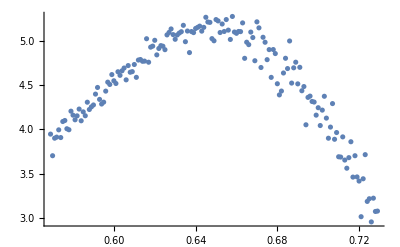

```mathematica
ListPlot[Take[SusceptData,{270, 430}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{270,430}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{{A,1.4},Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{5.14728 ⅇ^(-62.6407 (-0.642346+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 5.14728 | 0.0177679 | 289.695 | 2.78572×10^-217
Sigma | 0.0893422 | 0.00100425 | 88.9637 | 7.01863×10^-137
mu | 0.642346 | 0.000488906 | 1313.84 | 5.79218732047603×10^-321}

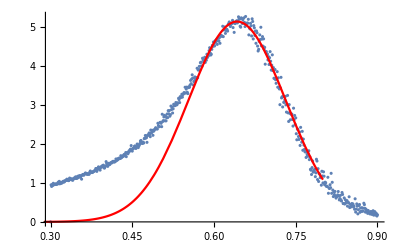

```mathematica
Show[ListPlot[SusceptData, PlotRange->Full],Plot[SusceptFit[x],{x,0,0.8},PlotRange->{{0,0.8},{0,500}}, PlotStyle->Red]]
```

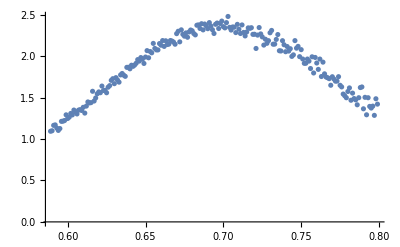

```mathematica
ListPlot[Take[CvData,{290,500}]]
```

```mathematica
CvFit = NonlinearModelFit[Take[CvData,{290,500}],A*Exp[-( x-mu)^2/(2*Sigma^2)],{A,Sigma,mu},x]
```

FittedModel[2.347 ⅇ^(-62.4595 (-«19»+x)^2)]

```mathematica
CvFit[{"BestFit","ParameterTable"}]
```

{2.347 ⅇ^(-62.4595 (-0.700733+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 2.347 | 0.00657632 | 356.887 | 6.62764×10^-292
Sigma | -0.0894717 | 0.000535872 | -166.965 | 1.51676×10^-223
mu | 0.700733 | 0.000333837 | 2099.03 | 6.90476720949859×10^-452}

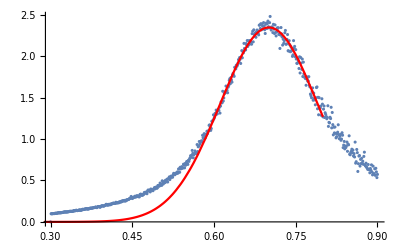

```mathematica
Show[ListPlot[CvData],Plot[CvFit[x],{x,0,0.8},PlotRange->Full,PlotStyle->Red]]
```